```mathematica
(*General utils*)
ParallelMapThread[f_,args_]:=ParallelMap[f@@#&,Transpose@args];
ParallelEvaluate@Off[FindMinimum::cvmit];
Options[ListLinePlot3D]={"Opacity"->1,"Size"->Thin,"Color"->Gray};
ListLinePlot3D[list_,OptionsPattern[]]:=
Show[Graphics3D[{Opacity[OptionValue["Opacity"]],OptionValue["Size"],OptionValue["Color"],Line[Table[#[[t]],{t,1,Length@#}]]}&/@list]]
```

# Fixed point finding functions

```mathematica
(*Adds noise gaussian noise of sd=<sd> to data*)
Noisy[data_,sd_:0.5]:=If[sd==0,data,data+RandomVariate[NormalDistribution[0,sd],Dimensions@data]]
```

```mathematica
(*Explicit expression of a GRU step*)
GruStep[s_,x_,gru_]:=Module[
{Wix,Wis,bi,Wrx,Wrs,br,Wmx,Wms,bm,i,r,m},
{Wix,Wis,bi,Wrx,Wrs,br,Wmx,Wms,bm}=Normal@Values@NetExtract[gru,"Arrays"];
i=LogisticSigmoid[Wix.x+Wis.s+bi];
r=LogisticSigmoid[Wrx.x+Wrs.s+br];
m=Tanh[Wmx.x+r*(Wms.s)+bm];
(1-i)*m+i*s
]
```

```mathematica
(*Function that runs a NetStateObject on <input> and records the state at every step*)
RunGru[GRUStateObject_,input_]:=Table[First@GRUStateObject[{input[[i]]}],{i,1,Length[input]}]
```

```mathematica
(*Loss function for finding the fixed points of <gru> dynamics under <input>*)
Speed[function_,s_]:=SquaredEuclideanDistance[s,function[s]];
```

```mathematica
(*Return linearisations around <fp> when constant <input> to RNN*)
Jacobians[points_,input_,gru_]:=With[{X=Array[x,Length@First@points]},D[GruStep[X,input,gru],{X}]/.Thread[X->#]&/@points];
```

```mathematica
(*True if jacobian has at least one positive real part eigenvalue*)
UnstableQ[jacobians_]:=If[Max@Abs@Eigenvalues@#>1,True,False]&/@jacobians
```

```mathematica
(*Affine function corresponding to dense layer <lin>*)
Wout[s_,lin_]:=With[
{W=Normal@NetExtract[lin,"Arrays"]["Weights"],b=Normal@NetExtract[lin,"Arrays"]["Biases"]},
W.s+b
]
```

```mathematica
(*Finds the fixed (slow) points of the dynamics described by <f> starting at <initPoints>*)
ClearAll[FindFixedPoints]
Options[FindFixedPoints]={"SpeedThreshold"->0.00001,"NormThreshold"->5,"UniqueThreshold"->0.025,"Method"->Automatic};
FindFixedPoints[
f_,
initPoints_,
OptionsPattern[]
]:=Module[
{
X=Array[x,Length@First@initPoints],
fps
},
fps=WaitAll@ParallelTable[(*Wait for all parallel computations to finish because it does some wierd stuff otherwise*)
FindMinimum[
Speed[f,X],
Transpose[{X,initPoints[[l]]}],
PrecisionGoal->5,
AccuracyGoal->5,
Method->OptionValue["Method"]
],{l,1,Length@initPoints,1}];
fps=Values@Last@#&/@Select[fps,First[#]<OptionValue["SpeedThreshold"]&];
fps=DeleteDuplicates[fps,EuclideanDistance[#1,#2]<OptionValue["UniqueThreshold"]&];
fps=Select[fps,Norm[#]<OptionValue["NormThreshold"]&]
]
```

```mathematica
(*General pipeline*)
ClearAll[GruFixedPointsPipeline]
Options[GruFixedPointsPipeline]={"Method"->Automatic,"Encoder"->(#&),"Checkpointing"->None,"TimeGoal"->60,"ValidationRatio"->0.1,"GradientClipping"->1,"L2Regularization"->0.00002,"NoiseFixedPointFinder"->0.5,"SpeedThreshold"->0.00001,"NormThreshold"->5};
GruFixedPointsPipeline[net_,trainingData_,samplingRunInputs_,fixedPointsFinderInputs_,OptionsPattern[]]:=
Module[
{training,trainedNet,gru,out,samplingRun,startingPoints,fixedPoints,fixedPointsJacobians},
training=NetTrain[
net,
trainingData,
All,
TrainingProgressCheckpointing->
If[OptionValue["Checkpointing"]==None,None,{"Directory","/home/leko/Documents/H21/MAT6115/finalproject/nets","Interval"->Quantity[OptionValue["Checkpointing"],"Rounds"]}],
TimeGoal->OptionValue["TimeGoal"],
ValidationSet->Scaled[OptionValue["ValidationRatio"]],
Method->{"ADAM","GradientClipping"->OptionValue["GradientClipping"],"L2Regularization"-> OptionValue["L2Regularization"]}
];
trainedNet=training["TrainedNet"];
{gru,out}=Information[trainedNet,"LayersList"];
samplingRun=
RunGru[
NetStateObject@gru,
samplingRunInputs
];
startingPoints=Noisy[samplingRun,OptionValue["NoiseFixedPointFinder"]];
fixedPoints=
Table[
Quiet@FindFixedPoints[
GruStep[#,fixedPointsFinderInputs[[j]],gru]&,
startingPoints,
"Method"->OptionValue["Method"],
"SpeedThreshold"->OptionValue["SpeedThreshold"],
"NormThreshold"->OptionValue["NormThreshold"]
],{j,1,Length@fixedPointsFinderInputs,1}
];
fixedPointsJacobians=ParallelMapThread[
Jacobians[#1,#2,gru]&,
{
fixedPoints,
fixedPointsFinderInputs
}
];
<|"TrainingResults"->training,"Net"->trainedNet,"FixedPoints"->fixedPoints,"SamplingRun"->samplingRun,"FixedPointsJacobians"->fixedPointsJacobians,"PrincipalComponents"->PrincipalComponents[samplingRun],"FixedPointsInputs"->fixedPointsFinderInputs,"Encoder"->OptionValue["Encoder"]|>
]
```

```mathematica
Internals[flipFlop_,input_,X_]:=Module[
{Wix,Wis,bi,Wrx,Wrs,br,Wmx,Wms,bm,i,r,m,s,
internals},
{Wix,Wis,bi,Wrx,Wrs,br,Wmx,Wms,bm}=Normal@Values@NetExtract[NetExtract[flipFlop["Net"],1],"Arrays"];
i=LogisticSigmoid[Wix.input+Wis.X+bi];
r=LogisticSigmoid[Wrx.input+Wrs.X+br];
m=Tanh[Wmx.input+r*(Wms.X)+bm];
s=(1-i)*m+i*X;
internals=<|"Wix"->Wix,"bi"->bi,"Wrx"->Wrx,"Wrs"->Wrs,"br"->br,"Wmx"->Wmx,"Wms"->Wms,"bm"->bm,"i"->i,"r"->r,"m"->m,"s"->s|>
]
```

```mathematica
FindCheckpointsFps[trainingObject_,inputs_]:=Module[
{
grus=Part[NetExtract[#,1]&
/@Import
/@trainingObject["CheckpointingFiles"],;;200],
initPoints
},
initPoints=Noisy@
RunGru[
NetStateObject@Last@grus,
inputs
];
Outer[
FindFixedPoints[
#1,
#2,
initPoints
]&,
grus,
Tuples[{0,-1,1},2],
1,1
]
];
```

```mathematica
ClearAll[InternalsTrajectory]
InternalsTrajectory[flipFlop_,inputTraj_,internal_]:=
With[{hiddenTraj=RunGru[NetExtract[flipFlop["Net"],1],inputTraj]},
ParallelMapThread[
Internals[flipFlop,#1,#2][internal]&,
{inputTraj,hiddenTraj}
]
];
```

```mathematica
Unprotect[PrincipalComponents];
PrincipalComponents[data_]:=With[{eigensystem=Eigensystem@Covariance@Standardize@data},
<|"PrincipalComponents"->eigensystem[[2,All]],
"VarianceExplained"->(#/Total@eigensystem[[1]]&/@eigensystem[[1]])|>]
```

```mathematica
(*isshh*)
FlipFlopReconstructedOutputPlot[flipFlop_]:=Module[
{reversePCA,lin,samplePoints,reconstructedOutput},
reversePCA=DimensionReduction[flipFlop["SamplingRun"],2,"PrincipalComponentsAnalysis"][#,"OriginalData"]&;
lin=NetExtract[NetExtract[flipFlop["Net"],2],"Net"];
reconstructedOutput[point_]:=First@Ordering[
EuclideanDistance[
Wout[reversePCA[point],lin]
,#
]&/@Tuples[{-1,1},2],
{-1}];
ListDensityPlot[Level[ParallelTable[{x,y,reconstructedOutput[{x,y}]},{x,-4,4,0.2},{y,-4,4,0.2}],{-2}],InterpolationOrder->1,ClippingStyle->Automatic]
]
```

# Visualization functions

```mathematica
(*Rescale a line while keeping origin fixed*)
RescaleLine[line_,newLength_]:=With[
{
m=Midpoint[line],
p1=First@line,
p2=Last@line,
l=Norm[Last@line-First@line]
},
{m+(p1-m)*newLength/l,m+(p2-m)*newLength/l}
]
```

```mathematica
(*Returns lines corresponding to first two eigenvectors subspaces*)
Options[EigenvectorPlot]={"nLines"->2,"Lenght"->0.5};
EigenvectorPlot[flipFlop_,inputIndex_,OptionsPattern[]]:=Module[
{
fpsFlat=Level[flipFlop["FixedPoints"][[inputIndex]],{-2}],
jacobiansFlat=Level[flipFlop["FixedPointsJacobians"][[inputIndex]],{-3}],
PCA=DimensionReduction[flipFlop["SamplingRun"],2],
fpsMainEV
},
fpsMainEV=Chop@Transpose/@
(Eigensystem/@jacobiansFlat)[[All,All,;;OptionValue["nLines"]]];
Graphics@Flatten[
Table[
{Which[-1.0<Re@First@#<-0.9||Im@First@#>0.2,Green,Abs@First@#<0.90,Red,Abs@First@#>1.1,Blue,True,Yellow],Line[RescaleLine[PCA@{fpsFlat[[i]]-Re@Last@#,fpsFlat[[i]]+Re@Last@#},OptionValue["Lenght"]]]}(*Last and First because # fpsMainEV[[i]] is a pair{ev,eV}*)
&/@fpsMainEV[[i]],
{i,1,Length@fpsFlat}
],
1]
]
(*Same thing in 3D*)
Options[EigenvectorPlot3D]={"nLines"->3,"Lenght"->0.5};
EigenvectorPlot3D[flipFlop_,inputIndex_,OptionsPattern[]]:=Module[
{
fpsFlat=Level[flipFlop["FixedPoints"][[inputIndex]],{-2}],
jacobiansFlat=Level[flipFlop["FixedPointsJacobians"][[inputIndex]],{-3}],
PCA=DimensionReduction[flipFlop["SamplingRun"],3,Method->"PrincipalComponentsAnalysis"],
fpsMainEV
},
fpsMainEV=Chop@Transpose/@
(Eigensystem/@jacobiansFlat)[[All,All,;;OptionValue["nLines"]]];
Graphics3D@Flatten[
Table[
{If[Re@First@#>1,Blue,Red],Thick,Line[RescaleLine[PCA@{fpsFlat[[i]]-Re@Last@#,fpsFlat[[i]]+Re@Last@#},OptionValue["Lenght"]]]}
&/@fpsMainEV[[i]],
{i,1,Length@fpsFlat}
],
1]
]
```

```mathematica
(*Shows the fixed points projected onto top 2 PCA of dynamics*)
ClearAll[FixedPointPlot]
Options[FixedPointPlot]={"DimensionReductionMethod"->"PrincipalComponentsAnalysis","Opacity"->1,"Size"->0.01};
FixedPointPlot[flipFlop_,inputIndex_,OptionsPattern[]]:=
Module[
{
PCA=DimensionReduction[flipFlop["SamplingRun"],2,Method->OptionValue["DimensionReductionMethod"]]
},
Show[
ListPlot[(*Plots ALL the fixed points*)
{#}&/@Level[PCA/@flipFlop["FixedPoints"][[inputIndex]],{-2}],
PlotStyle->
(Directive[
If[#==True,Blue,Red],
PointSize@OptionValue["Size"],
Opacity[OptionValue["Opacity"]]]&/@Flatten@(UnstableQ/@Level[flipFlop["FixedPointsJacobians"][[inputIndex]],{-4}])),
PlotRange->Full]
]
]
(*Same thing inShows the fixed points projected onto top 4 PCA of dynamics*)
ClearAll[FixedPointPlot3D]
Options[FixedPointPlot3D]={"DimensionReductionMethod"->"PrincipalComponentsAnalysis","Opacity"->1,"Size"->0.01};
FixedPointPlot3D[flipFlop_,inputIndex_,OptionsPattern[]]:=
Module[
{
PCA=DimensionReduction[flipFlop["SamplingRun"],3,Method->OptionValue["DimensionReductionMethod"]]
},
Show[
ListPointPlot3D[(*Plots ALL the fixed points*)
{#}&/@Level[PCA/@flipFlop["FixedPoints"][[inputIndex]],{-2}],
PlotStyle->
(Directive[
If[#==True,Blue,Red],
Opacity[OptionValue["Opacity"],
PointSize@OptionValue["Size"]
]]&/@Flatten@(UnstableQ/@Level[flipFlop["FixedPointsJacobians"][[inputIndex]],{-4}])),
PlotRange->Full
]
]
]
```

```mathematica
(*Show the evolution of the hidden state during evalutation of <sequence>*)
ClearAll[AnimateGruRun]
Options[AnimateGruRun]={"Noise"->0};
AnimateGruRun[flipFlop_,runInputs_,runHiddens_,ioPlot_,OptionsPattern[]]:=
Module[
{
PCA=DimensionReduction[flipFlop["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"],
fixedPointPlot,
pred,animationList,eigenvectorPlot
},
pred=NetDrop[flipFlop["Net"],1]@runHiddens;(*Only keep output part of the net and feed hidden states*)
fixedPointPlot=FixedPointPlot[flipFlop,All];
eigenvectorPlot=EigenvectorPlot[flipFlop,All];
animationList=ParallelTable[
GraphicsRow[
{
(*Dynamics of hiddenstate*)
Show[
(*Fixed point plot*)
fixedPointPlot,
(*Highlights the fixed points that are active*)
ListPlot[ 
If[#≠{},{#},Null]&/@
Level[Part[
PCA/@flipFlop["FixedPoints"],
Level[Position[flipFlop["FixedPointsInputs"],runInputs[[t]]],{-1}]
],{-2}],
PlotStyle->(If[#==True,Blue,Red]&/@
Level[Part[
UnstableQ/@flipFlop["FixedPointsJacobians"],
Level[Position[flipFlop["FixedPointsInputs"],runInputs[[t]]],{-1}]
],{-1}]),
PlotMarkers->{Graphics@Circle[], Medium}
],
eigenvectorPlot,
(*Current hidden state of the RNN*)
ListPlot[
{PCA@runHiddens[[t]]},
PlotStyle->{PointSize[0.05],Black}],

PlotRange->Full,
Boxed->False
],
(*IO Plot*)
ioPlot[runInputs,pred[[;;t]]]
}
],
{t,1,Length@runInputs,1}];
ListAnimate[animationList,1]
]
```

```mathematica
(*Shows the orbits of <initStates> under <inputs> projected on first 2 PCs. We can specify the fixed points to plot.*)
AnimateOrbit[flipFlop_,inputs_,initStates_,fixedPointIndexToPlot_]:=
Module[
{
trajectories,trajectoriesFunc
},
trajectories=
Join[(*Compute trajectory*)
{#},
RunGru[ 
NetStateObject[NetExtract[flipFlop["Net"],1],<|{"State"}:>#|>],
inputs
]
]&/@Level[initStates,{-2}];
trajectoriesFunc=
Interpolation[
Transpose@{Range[Length@inputs+1],DimensionReduction[flipFlop["SamplingRun"],2]@#}
]&/@trajectories;
ParallelTable[
Show[
ParametricPlot[#[t]&/@trajectoriesFunc,{t,1,tmax}],
FixedPointPlot[flipFlop,fixedPointIndexToPlot],
PlotRange->Full
]
,{tmax,1.001,Length@inputs+1}
]
]
AnimateOrbit3D[flipFlop_,inputs_,initStates_,fixedPointIndexToPlot_]:=
Module[
{
trajectories,trajectoriesFunc,fixedPointPlot
},
trajectories=
Join[(*Compute trajectory*)
{#},
RunGru[ 
NetStateObject[NetExtract[flipFlop["Net"],1],<|{"State"}:>#|>],
inputs
]
]&/@Level[initStates,{-2}];
trajectoriesFunc=
Interpolation[
Transpose@{Range[Length@inputs+1],DimensionReduction[flipFlop["SamplingRun"],3]@#}
]&/@trajectories;
fixedPointPlot=FixedPointPlot3D[flipFlop,fixedPointIndexToPlot];
ParallelTable[
Show[
ParametricPlot3D[#[t]&/@trajectoriesFunc,{t,1,tmax}],
fixedPointPlot,
PlotRange->Full
]
,{tmax,1.001,Length@inputs+1}
]
]
```

```mathematica
(*Plot all the trajectories of all states in <initStates> on <>*)
ClearAll[TrajectoriesPlot]
Options[TrajectoriesPlot]={"Opacity"->0.5,"Color"->Gray,"Size"->Thin};
TrajectoriesPlot[flipFlop_,inputs_,initStates_,OptionsPattern[]]:=
Module[
{
trajectories,trajectoriesFunc
},
trajectories=
Join[(*Compute trajectory*)
{#},
RunGru[ 
NetStateObject[NetExtract[flipFlop["Net"],1],<|{"State"}:>#|>],
inputs
]
]&/@Level[initStates,{-2}];
Show[
ListLinePlot[
DimensionReduction[flipFlop["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"]/@trajectories,
PlotStyle->Directive[OptionValue["Color"],OptionValue["Size"],Opacity[OptionValue["Opacity"]]], PlotRange->Full],
PlotRange->{{-6,6},{-6,6}}
]
]
ClearAll[TrajectoriesPlot3D]
Options[TrajectoriesPlot3D]={"Opacity"->0.5,"Size"->Thick};
TrajectoriesPlot3D[flipFlop_,inputs_,initStates_,OptionsPattern[]]:=
Module[
{
trajectories,trajectoriesFunc
},
trajectories=
Join[(*Compute trajectory*)
{#},
RunGru[ 
NetStateObject[NetExtract[flipFlop["Net"],1],<|{"State"}:>#|>],
inputs
]
]&/@Level[initStates,{-2}];
Show[
ListLinePlot3D[DimensionReduction[flipFlop["SamplingRun"],3]/@trajectories,"Opacity"->OptionValue["Opacity"],"Size"->OptionValue["Size"]],
PlotRange->{{-5,5},{-5,5},{-5,5}}
]
]
```

```mathematica
(*isshh*)
ClearAll[ReconstructedOutputRegions]
ReconstructedOutputRegions[flipFlop_,outputStates_]:=Module[
{reversePCA,lin,samplePoints,pred,PCA2Pred},
reversePCA=DimensionReduction[flipFlop["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"][#,"OriginalData"]&;
lin=NetExtract[NetExtract[flipFlop["Net"],2],"Net"];
PCA2Pred[pcaPoint_]:=First@Ordering[
Table[
EuclideanDistance[Wout[reversePCA[pcaPoint],lin],outputStates[[i]]],
{i,1,Length@outputStates,1}
]];
ListDensityPlot[Level[ParallelTable[{x,y,PCA2Pred[{x,y}]},{x,-5,5,0.1},{y,-5,5,0.1}],{-2}],(*InterpolationOrder->1,ClippingStyle->Automatic,*)PlotLegends->Automatic]
]
```

# Fixed point analysis k-FlipFlop

## Functions

```mathematica
ClearAll[FlipFlopInput,FlipFlopTrainingData,FlipFlopNet,FlipFlopPipeline]
```

```mathematica
Options[FlipFlopInput]={"PossibleStates"->{1,-1}};
(*Input stream for FlipFlop task*)
FlipFlopInput[n_,timeSteps_,nBits_,pFlip_,OptionsPattern[]]:=Join[Table[0,n,1,nBits],RandomChoice[Join[Table[pFlip/(Length@OptionValue["PossibleStates"]),(Length@OptionValue["PossibleStates"])],{1-pFlip}]->Join[OptionValue["PossibleStates"],{0}],{n,timeSteps-1,nBits}],2];
```

```mathematica
(*Training data for k-FlipFlop problem. Has options for noise and delay.*)
Options[FlipFlopTrainingData]={"Noise"->0,"Delay"->0,"PossibleStates"->{1,-1}};
FlipFlopTrainingData[n_,timeSteps_,nBits_,pFlip_,OptionsPattern[]]:=Module[
{
input=FlipFlopInput[n,timeSteps,nBits,pFlip,"PossibleStates"->OptionValue["PossibleStates"]],
output = Table[1,n,timeSteps,nBits],
b,s,t
},
For[b=1,b≤ n,b++,
For[s=1,s≤nBits,s++,
For[t=2,t≤ timeSteps,t++,
If[input[[b,t,s]]== 0,
output[[b,t,s]]=output[[b,t-1,s]],
output[[b,t,s]]=input[[b,t,s]]
]]]
];
If[OptionValue["Delay"]≠ 0,output=Join[Table[1,n,OptionValue["Delay"],nBits],output,2][[All,;;timeSteps,All]]];
Table[Noisy[input[[i]],OptionValue["Noise"]]-> output[[i]],{i,1,n}]
];
```

```mathematica
(*Definition of the net configuration for k-FlipFlop problem.*)
FlipFlopNet[inputSize_,outputSize_,hiddenSize_]:=
NetChain[
{
GatedRecurrentLayer[hiddenSize],(*GRU layer*)
NetMapOperator[LinearLayer[outputSize]](*Linear output layer*)
}
,"Input"->{"Varying",inputSize}]
```

```mathematica
(*Shorthand to the general pipeline*)
FlipFlopPipeline[nTrainingExamples_,timeSteps_,nBits_,pFlip_,hiddenSize_,trainingTime_,noise_,delay_,nStartingPointsFixedPoints_,fixedPointFinderInputs_,possibleState_:{1,-1}]:=
GruFixedPointsPipeline[
FlipFlopNet[nBits,nBits,hiddenSize],
FlipFlopTrainingData[nTrainingExamples,timeSteps,nBits,pFlip,"Noise"->noise,"Delay"->delay],
First@FlipFlopInput[1,nStartingPointsFixedPoints,nBits,pFlip],
fixedPointFinderInputs,
"TimeGoal"->trainingTime
]
```

```mathematica
(*Plots the IO of the evaluation of <flipFlop> on inputs*)
FlipFlopIOPlot[nBits_,inputs_,outputs_]:=
GraphicsColumn[(*Plots the I/O of the RNN*)
Table[
ListLinePlot[{inputs[[All,bit]],outputs[[All,bit]]},PlotRange->{-1.2,1.2}],
{bit,1,nBits}
]
]
```

```mathematica
Options[AnimateFlipFlop]={"Noise"->0,"PossibleStates"->{-1,1}};
AnimateFlipFlop[flipFlop_,timeSteps_,pFlip_,OptionsPattern[]]:=Module[
{inputs,
hiddens},
inputs=Noisy[First@FlipFlopInput[1,timeSteps,2,pFlip,"PossibleStates"->OptionValue["PossibleStates"]],OptionValue["Noise"]];
hiddens=RunGru[NetStateObject[NetExtract[flipFlop["Net"],1]],inputs];
AnimateGruRun[flipFlop,inputs,hiddens,FlipFlopIOPlot[2,#1,#2]&]
]
```

## 3-FlipFlop

```mathematica
(*Training a GRU to accomplish the 3-FlipFlop task and searching for fixed points of underlying dynamics*)
(*simple3FlipFlop=FlipFlopPipeline[
256,(*Number of training examples*)
64,(*Time steps*)
3,(*Number of bits*)
0.5,(*Probability of flip every time steps*)
16,(*Hidden size*)
60,(*Training time*)
0,(*Noise*)
0,(*Delay*)
512,(*Number of starting points to find fixed points*)
Tuples[{0,-1,1},3](*Inputs according to which to find the fixed points*)
];*)
```

```mathematica
simple3FlipFlop=Import["simple3FlipFlop.mx"];
```

```mathematica
(*Variance explained by principal components*)
ListLinePlot[simple3FlipFlop["PrincipalComponents"]["VarianceExplained"],AxesLabel->{"PC","% of variance explained"}]
```

## 2-FlipFlop

```mathematica
(*simple2FlipFlop=FlipFlopPipeline[
256,(*Number of training examples*)
64,(*Time steps*)
2,(*Number of bits*)
0.5,(*Probability of flip every time steps*)
16,(*Hidden size*)
60,(*Training time*)
0,(*Noise*)
0,(*Delay*)
512,(*Number of starting points to find fixed points*)
Tuples[{0,-1,1},2](*Inputs according to which to find the fixed points*)
];*)
```

```mathematica
(*Data used for paper*)
simple2FlipFlop=Import["simple2FlipFlop.mx"];
```

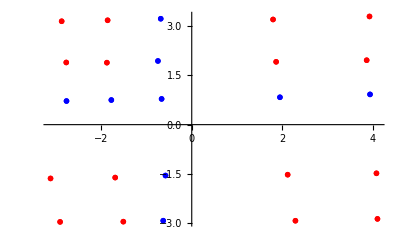

```mathematica
FixedPointPlot[simple2FlipFlop,All]
```

```mathematica
Export["2flipfloprun.mp4",AnimateFlipFlop[simple2FlipFlop,50,0.2]]
```

2flipfloprun.mp4

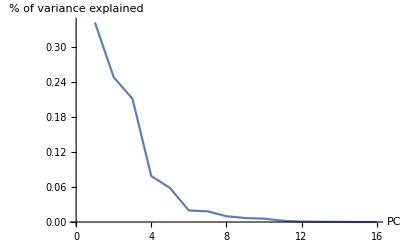

```mathematica
(*Variance explained by principal components*)
ListLinePlot[simple2FlipFlop["PrincipalComponents"]["VarianceExplained"],AxesLabel->{"PC","% of variance explained"}]
```

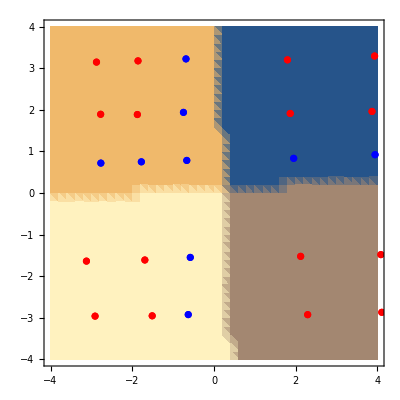

```mathematica
(*Region of PCA space corresponding to every output*)
Show[FlipFlopReconstructedOutputPlot[simple2FlipFlop],FixedPointPlot[simple2FlipFlop]]
```

## 2-FlipFlop noise resistance and effects of training with noise

```mathematica
noisy2FlipFlops=Map[
FlipFlopPipeline[
512,(*Number of training examples*)
64,(*Time steps*)
2,(*Number of bits*)
0.5,(*Probability of flip every time steps*)
20,(*Hidden size*)
2*60,(*Training time*)
#,(*Noise*)
0,(*Delay*)
512,(*Number of starting points to find fixed points*)
{{0,0}}(*Inputs according to which to find the fixed points*)
]&,
Table[#,5]&/@Range[0,0.15,0.025],
{2}
];
```

```mathematica
noisyEvalsAbs=Abs/@Flatten/@Map[Eigenvalues/@#["FixedPointsJacobians"][[1]]&,noisy2FlipFlops,{2}];
```

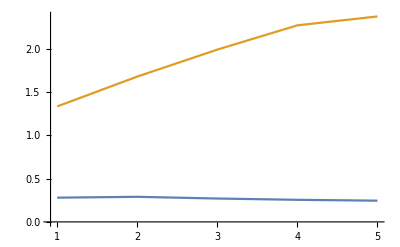

```mathematica
{Table[Mean@Select[noisyEvalsAbs[[i]],#<1&],{i,1,5,1}],Table[Mean@Select[noisyEvalsAbs[[i]],#>1&],{i,1,5,1}]}//ListLinePlot[#,PlotRange->Full]&
```

```mathematica
fps=FindFixedPoints[GruStep[#,{0,0.1},NetExtract[noisy2FlipFlops[[5,1]]["Net"],1]]&,Noisy@noisy2FlipFlops[[5,1]]["SamplingRun"]];
```

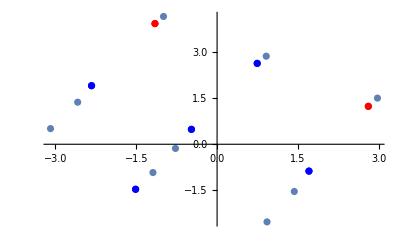

```mathematica
Show[ListPlot[DimensionReduction[noisy2FlipFlops[[5,1]]["SamplingRun"],2]@fps],FixedPointPlot[noisy2FlipFlops[[5,1]],All]]
```

```mathematica
AnimateFlipFlop[noisy2FlipFlops[[5,1]],20,0.1,"Noise"->0.1]
```

## 2-FlipFlop with increasing delay

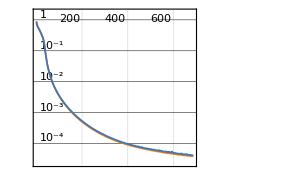
<|TrainingResults→NetTrainResultsObject[NetTrain Results
summary | ,,  batches:9625  rounds:687  time:2.0min  examples/s:2566
data | ,,  training examples:448  validation examples:64  processed examples:308000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:3.91×10^-5
validation | ,,  loss:4.11×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ],Net→NetChain[<>],FixedPoints→{1},SamplingRun→1,1,PrincipalComponents→<|PrincipalComponents→{{0.00812681,0.239072,-0.0772212,0.140112,0.367478,-0.137911,0.16438,0.0910283,0.365551,0.263532,0.0649312,0.160437,0.0870861,0.223073,-0.140617,0.116142,-0.0977358,-0.173023,-0.141694,0.35205,0.173371,-0.196257,-0.362678,0.143396},22,{1}},V…ed→1|>,FixedPointsInputs→{{0,0},{0,-1},{0,1},{-1,0},{-1,-1},{-1,1},{1,0},{1,-1},{1,1}},Encoder→(#1&)|>
 |  |  |  |

```mathematica
flipFlopDelay5=FlipFlopPipeline[
512,(*Number of training examples*)
64,(*Time steps*)
2,(*Number of bits*)
0.5,(*Probability of flip every time steps*)
24,(*Hidden size*)
2*60,(*Training time*)
0,(*Noise*)
3,(*Delay*)
1024,(*Number of starting points to find fixed points*)
Tuples[{0,-1,1},2](*Inputs according to which to find the fixed points*)]
```

```mathematica
delayFlipFlops=Import["delayFlipFlops.mx"];
```

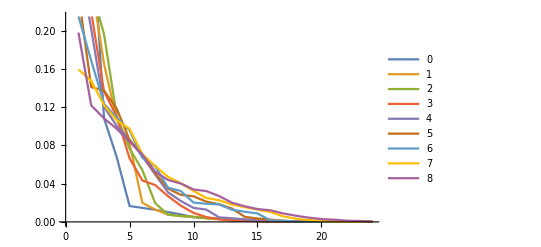

```mathematica
(*Variance explained first 5 PCs*)
#["PrincipalComponents"]["VarianceExplained"]&/@delayFlipFlops//ListLinePlot[#,PlotLegends->Range[0,Length@delayFlipFlops]]&
```

```mathematica
AnimateFlipFlop[flipFlopDelay5,30,0.2]
```

```mathematica
Export["delayflipfloprun.mp4",AnimateFlipFlop[flipFlopDelay5,50,0.2]]
```

delayflipfloprun.mp4

## Formation/evolution of fixed points

```mathematica
fps=Import["BIGfps.mx"];
plot=Import["BIGfpsPlot.mx"];
trained=Import["BIGtrain.mx"];
```

```mathematica
grus=NetExtract[#,1]&/@(Import[#]&/@trained["CheckpointingFiles"]);
lins=NetExtract[NetExtract[#,2],"Net"]&/@(Import[#]&/@trained["CheckpointingFiles"]);
```

```mathematica
inputs=First@FlipFlopInput[1,300,2,0.5];
hiddens=
RunGru[
NetStateObject@Last@grus,
inputs
];
```

```mathematica
ListAnimate[plot,5]
```

```mathematica
Export["bifurcations.mp4",%91]
```

bifurcations.mp4

# Fixed point analysis DFAs

## Functions

```mathematica
DFA[states_,alphabet_,transitionFun_,startState_]:=<|"States"->states,"Alphabet"->alphabet,"TransitionFunction"->transitionFun,"StartState"->startState|>;
```

```mathematica
(*Definition of the net configuration for k-FlipFlop problem.*)
ClearAll[DFANet]
Options[DFANet]={"Encoder"->True,"Decoder"->True};
DFANet[DFA_,hiddenSize_,OptionsPattern[]]:=
With[
{encoder=Replace[
OptionValue["Encoder"],
{
True:>NetEncoder[{"Class",DFA["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}],
False:>{"Varying",Length@First@DFA["Alphabet"]}
}
],
decoder=
Replace[
OptionValue["Decoder"],
{
True:>NetDecoder[{"Class",DFA["States"]}],
False:>{"Varying",Length@First@DFA["States"]}
}
]
},
NetChain[
{
GatedRecurrentLayer[hiddenSize],(*GRU layer*)
NetMapOperator[LinearLayer[If[OptionValue["Decoder"],Length@DFA["States"],Length@First@DFA["States"]]]](*Linear output layer*)
},
"Input"->encoder,
"Output"->decoder
]
]
```

```mathematica
ClearAll[DFATrainingData]
Options[DFATrainingData]={"Decoder"->True};
DFATrainingData[DFA_,inputs_,OptionsPattern[]]:=
Module[
{
f=DFA["TransitionFunction"],
enc=Replace[
OptionValue["Decoder"],
{
True:>NetEncoder[{"Class",DFA["States"],"UnitVector"}],
False:> (#&)}
]
},
Table[inputs[[i]]->enc[Rest@FoldList[f,DFA["StartState"],inputs[[i]]]],{i,1,Length@inputs}]
]
```

```mathematica
ClearAll[DFAPipeline]
Options[DFAPipeline]={"Encoder"->True,"Decoder"-> True,"Method"->Automatic,"SpeedThreshold"->0.00001,"NormThreshold"->5,"NoiseFixedPointFinder"->0.5};
DFAPipeline[DFA_,hiddenSize_,inputs_,trainingTime_,startingPointsInputs_,fixedPointFinderInputs_,OptionsPattern[]]:=
With[
{enc=If[OptionValue["Encoder"],NetEncoder[{"Class",DFA["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}],(#&)]},
GruFixedPointsPipeline[
DFANet[DFA,hiddenSize,"Encoder"->OptionValue["Encoder"],"Decoder"->OptionValue["Decoder"]],
DFATrainingData[DFA,inputs,"Decoder"->OptionValue["Decoder"]],
enc@startingPointsInputs,
enc@fixedPointFinderInputs,
"TimeGoal"->trainingTime,
"Method"->OptionValue["Method"],
"SpeedThreshold"->OptionValue["SpeedThreshold"],
"NormThreshold"->OptionValue["NormThreshold"],
"NoiseFixedPointFinder"->OptionValue["NoiseFixedPointFinder"]
]
]
```

```mathematica
ClearAll[AnimateDFA]
AnimateDFA[DFA_,DFAgru_,inputs_,encoder_:True]:=Module[
{
hiddens,
enc=If[encoder,NetEncoder[{"Class",DFA["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}],(#&)]
},
hiddens=RunGru[NetStateObject[NetExtract[DFAgru["Net"],1]],enc@inputs];
AnimateGruRun[DFAgru,enc@inputs,hiddens,Function[{x},Null]]
]
```

```mathematica
?FlipFlopIOPlot
```

## Flip-Flop DFAs

```mathematica
dfaFlipFlop=DFA[
Tuples[{-1,1},2],
Tuples[{0,-1,1},2],
Function[{state,input},MapThread[If[#2==0,#1,#2]&,{state,input}]],
{1,1}
];
```

```mathematica
flipFlopEncoded=Import["flipFlopEncoded.mx"];
flipFlop12=Import["flipFlop12.mx"];
```

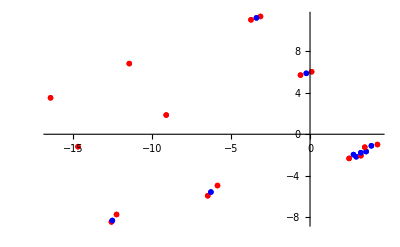

```mathematica
FixedPointPlot[flipFlop12,All]
```

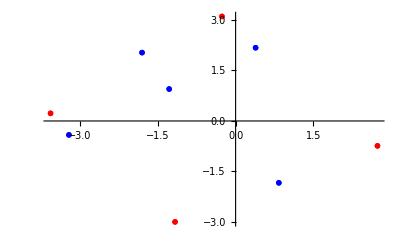

```mathematica
FixedPointPlot[flipFlopEncoded,1]
```

```mathematica
?AnimateDFA
```

```mathematica
AnimateDFA[dfaFlipFlop,flipFlopEncoded,First@FlipFlopInput[1,10,2,0.2]]
```

```mathematica
Export["12flipfloprun.mp4",%96]
```

12flipfloprun.mp4

## Modulo counting DFA

```mathematica
dfaModCount=
DFA[
{0,1,2},
{0,1},
Mod[#1+#2,3]&,
0
];
```

```mathematica
(*modCount=DFAPipeline[
dfaModCount,(*DFA corresponding to FlipFlop task*)
8,(*Hidden size*)
RandomChoice[{0.8,0.2}->dfaModCount["Alphabet"],{512,16}],(*Input for training data*)
60,(*Training time*)
RandomChoice[dfaModCount["Alphabet"],1024],(*Inputs to run the gru to get starting points for fixed point finding*)
dfaModCount["Alphabet"](*Input for which to find the fixed points*),
"Method"->"PrincipalAxis"
];*)
```

```mathematica
modCount=Import["modCount.mx"];
```

```mathematica
AnimateDFA[dfaModCount,modCount,{0,0,0,1,0,0,0,1,0,0,0,1,1,1,1,1,1,1,1}]
```

```mathematica
Export["modcountrun.mp4",%133]
```

modcountrun.mp4

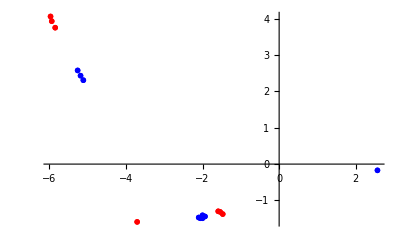

```mathematica
FixedPointPlot[modCount,All]
```

## Repeated sequence DFA

```mathematica
dfaRepeated=
DFA[
{"q0","q1","q2","q3"},
{0,1},
<|{"q0",0}->"q1",{"q0",1}->"q2",{"q1",1}->"q2",{"q1",0}->"q3",{"q2",1}->"q3",{"q2",0}->"q1",{"q3",0}->"q3",{"q3",1}->"q3"|>[{#1,#2}]&,
"q0"
];
```

```mathematica
(*repeated=DFAPipeline[
dfaRepeated,(*DFA corresponding to FlipFlop task*)
8,(*Hidden size*)
RandomChoice[dfaRepeated["Alphabet"],{512,16}],(*Input for training data*)
60,(*Training time*)
RandomChoice[dfaModCount["Alphabet"],1024],(*Inputs to run the gru to get starting points for fixed point finding*)
dfaModCount["Alphabet"](*Input for which to find the fixed points*),
"Method"->"PrincipalAxis",
"SpeedThreshold"->0.001
];*)
```

```mathematica
repeated=Import["repeated.mx"];
```

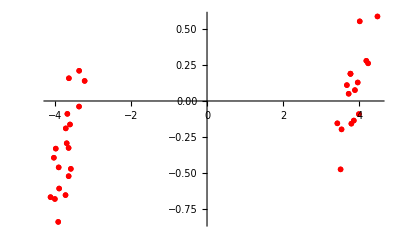

```mathematica
FixedPointPlot[repeated,All]
```

```mathematica
AnimateDFA[dfaRepeated,repeated,{0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0}]
```

```mathematica
Export["repeatedrun.mp4",%139]
```

repeatedrun.mp4

## Sequence identification

```mathematica
dfaSeqIdenfication=DFA[
{"q0","q1","q2","q3","q4"},
{0,1},
<|{"q0",0}->"q1",{"q0",1}->"q0",{"q1",0}->"q1",{"q1",1}->"q2",{"q2",0}->"q3",{"q2",1}->"q0",{"q3",0}->"q1",{"q3",1}->"q4",{"q4",0}->"q4",{"q4",1}->"q4"|>[{#1,#2}]&,
"q0"];
```

```mathematica
(*seqIdenfication=DFAPipeline[
dfaSeqIdenfication,(*DFA corresponding to FlipFlop task*)
8,(*Hidden size*)
RandomChoice[dfaSeqIdenfication["Alphabet"],{512,16}],(*Input for training data*)
60,(*Training time*)
RandomChoice[dfaSeqIdenfication["Alphabet"],1024],(*Inputs to run the gru to get starting points for fixed point finding*)
dfaSeqIdenfication["Alphabet"](*Input for which to find the fixed points*),
"Method"->"PrincipalAxis",
"SpeedThreshold"->0.001
];*)
```

```mathematica
seqIdentification=Import["seqIdentification.mx"];
```

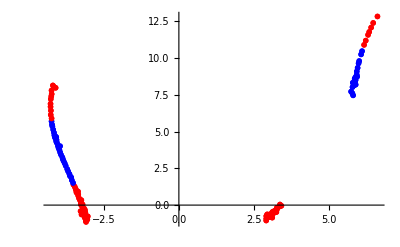

```mathematica
FixedPointPlot[seqIdentification,All]
```

```mathematica
AnimateDFA[dfaSeqIdenfication,seqIdentification,{1,1,1,1,1,0,1,0,0,1,0,1,0,1,0,1,1}]
```

```mathematica
Export["identificationrun.mp4",%146]
```

identificationrun.mp4

# Figures

```mathematica
(*Some figure*)
flipFlop3Traj=Show[
FixedPointPlot3D[simple3FlipFlop,All,"Opacity"->0.5],
FixedPointPlot3D[simple3FlipFlop,{1,#1},"Opacity"->1],
ListLinePlot3D[
{DimensionReduction[simple3FlipFlop["SamplingRun"],3]@
Join[
{simple3FlipFlop["FixedPoints"][[1,2]]},
RunGru[
NetStateObject[
NetExtract[simple3FlipFlop["Net"],1],
<|{"State"}:>simple3FlipFlop["FixedPoints"][[1,2]]|>
],{#2,{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}]
]},
"Size"->Thick,
"Color"->Green
],
TrajectoriesPlot3D[
simple3FlipFlop,
Table[{0,0,0},30],
Noisy[#,0.01]&@Level[Table[Pick[simple3FlipFlop["FixedPoints"][[1]],UnstableQ@First@simple3FlipFlop["FixedPointsJacobians"]],30],{-2}],
"Opacity"->0.7],
Boxed->False,
Axes->False
]&@@@{{3,{0,0,1}},{2,{0,0,-1}},{20,{1,0,-1}},{26,{1,1,-1}}}
(*Some other figure*)
flipflop3topo=Show[
FixedPointPlot3D[simple3FlipFlop,1],
EigenvectorPlot3D[simple3FlipFlop,1],
TrajectoriesPlot3D[simple3FlipFlop,Table[{0,0,0},30],Noisy[#,0.01]&@Level[Table[Pick[simple3FlipFlop["FixedPoints"][[1]],UnstableQ@First@simple3FlipFlop["FixedPointsJacobians"]],20],{-2}],"Opacity"->0.3,"Size"->Thick],
Boxed->False,
Axes->False
]
GraphicsGrid[{Join[{Show[flipflop3topo,ImageSize->Small],SpanFromLeft},flipFlop3Traj[[;;2]]],Join[{SpanFromAbove,SpanFromBoth},flipFlop3Traj[[3;;]]]},Frame->All,ImageSize->Full]
-Graphics-
```

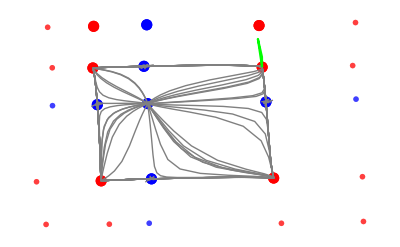
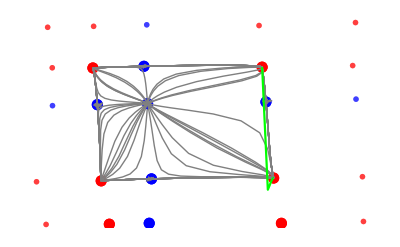
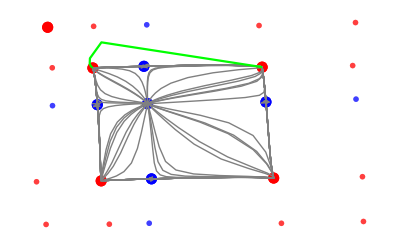
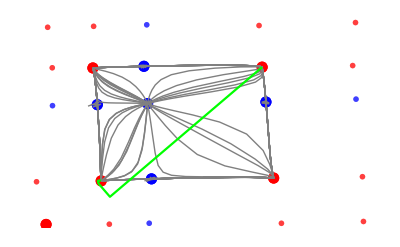
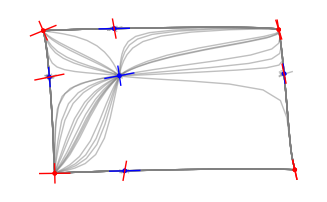
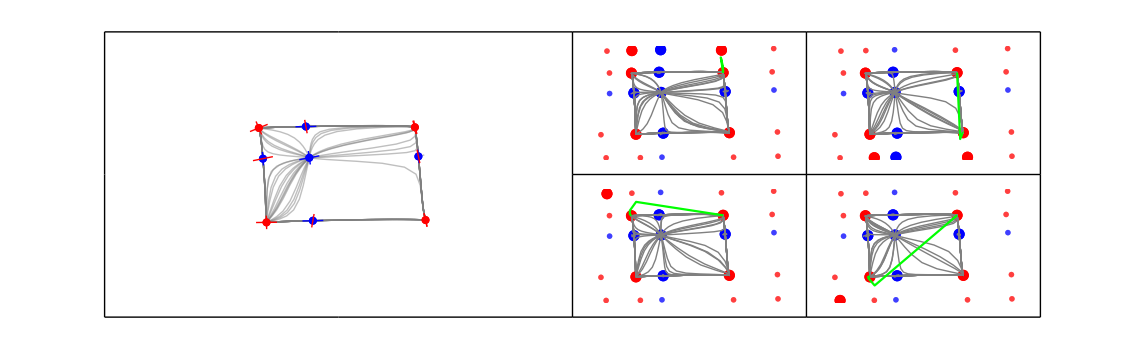
```mathematica
flipFlop2Traj=Show[
FixedPointPlot[simple2FlipFlop,All,"Opacity"->0.5],
FixedPointPlot[simple2FlipFlop,{1,#1},"Size"->0.02],
TrajectoriesPlot[
simple2FlipFlop,
Table[{0,0},30],
Noisy[#,0.01]&@Level[Table[Pick[simple2FlipFlop["FixedPoints"][[1]],UnstableQ@First@simple2FlipFlop["FixedPointsJacobians"]],30],{-2}],
"Opacity"->1],
ListLinePlot[
{DimensionReduction[simple2FlipFlop["SamplingRun"],2]@
Join[
{simple2FlipFlop["FixedPoints"][[1,2]]},
RunGru[
NetStateObject[
NetExtract[simple2FlipFlop["Net"],1],
<|{"State"}:>simple2FlipFlop["FixedPoints"][[1,2]]|>
],{#2,{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}]
]},
PlotStyle->Green,
PlotRange->Full
],
Boxed->False,
Axes->False
]&@@@{{3,{0,1}},{2,{0,-1}},{6,{-1,1}},{5,{-1,-1}}}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
flipFlop2Topo=Show[
TrajectoriesPlot[
simple2FlipFlop,
Table[{0,0},30],
Noisy[#,0.01]&@Level[Table[Pick[simple2FlipFlop["FixedPoints"][[1]],UnstableQ@First@simple2FlipFlop["FixedPointsJacobians"]],30],{-2}],
"Opacity"->0.5,
"Size"->Thick
],
FixedPointPlot[simple2FlipFlop,1],
EigenvectorPlot[simple2FlipFlop,1],
Axes->False,
PlotRange->All
]
-Graphics-
GraphicsGrid[{Join[{Show[flipFlop2Topo,ImageSize->Large],SpanFromLeft},flipFlop2Traj[[;;2]]],Join[{SpanFromAbove,SpanFromBoth},flipFlop2Traj[[3;;]]]},Frame->All,ImageSize->Large]
-Graphics-
```

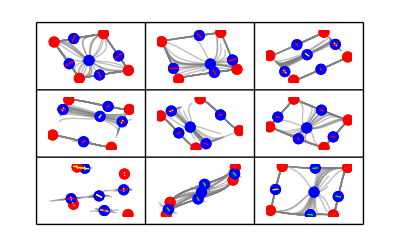
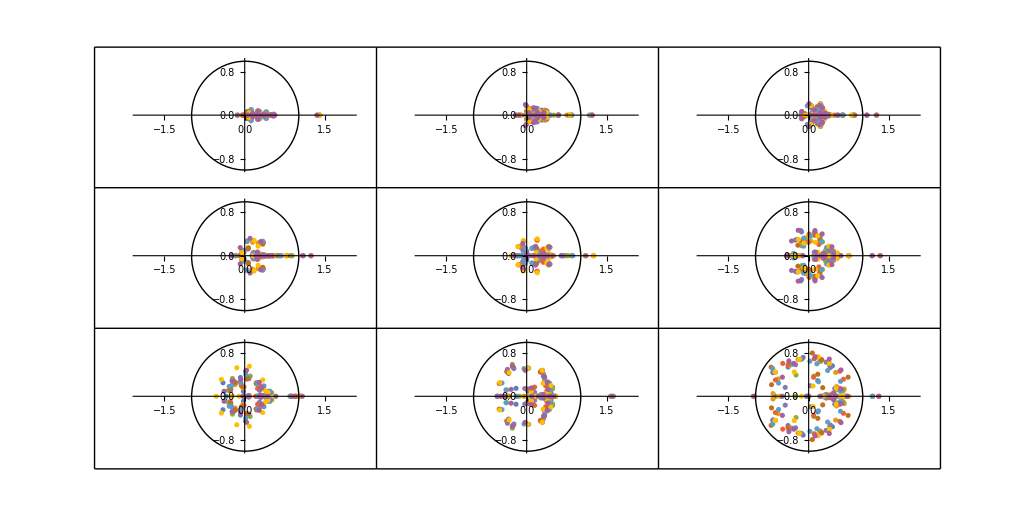
```mathematica
(*Fixed point topolgy*)
delayTopos=Show[
TrajectoriesPlot[
#,
Table[{0,0},30],
Noisy[#,0.01]&@Level[Table[Pick[#["FixedPoints"][[1]],UnstableQ@First@#["FixedPointsJacobians"]],30],{-2}],
"Opacity"->0.5,
"Size"->Thick
],
FixedPointPlot[#,1,"Size"->0.02],
EigenvectorPlot[#,1],
Axes->False,
PlotRange->All
]&/@delayFlipFlops
GraphicsGrid[ArrayReshape[delayTopos,{3,3}],Frame->All]
-Graphics-
(*Eigenvalues of the Jacobians of all fixed points*)
delayEigenvalues=Table[Map[Eigenvalues,delayFlipFlops[[i]]["FixedPointsJacobians"],{2}],{i,1,Length@delayFlipFlops}];
ArrayReshape[ParallelTable[
Show[
ComplexListPlot[#,PlotRange->{{-2,2},{-1,1}}],
Graphics@Circle[]
]&@delayEigenvalues[[i,1]],
{i,1,Length@delayFlipFlops,1}],{3,3}]//GraphicsGrid[#,Frame->All]&
-Graphics-
```

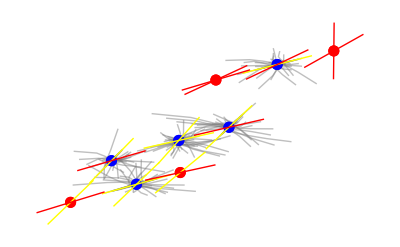
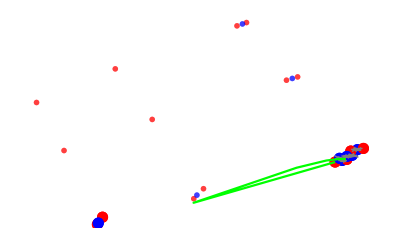
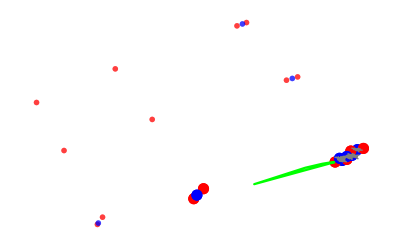
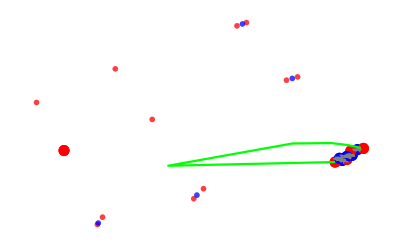
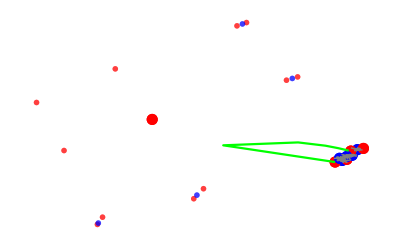
```mathematica
flipFlopEncodedTopo=Show[
TrajectoriesPlot[
#,
NetEncoder[{"Class",dfaFlipFlop["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@Table[{0,0},40],
Noisy[#,0.01]&@Level[Table[Pick[#["FixedPoints"][[1]],UnstableQ@First@#["FixedPointsJacobians"]],30],{-2}],
"Opacity"->0.5,
"Size"->Thick
],
FixedPointPlot[#,1,"Size"->0.02],
EigenvectorPlot[#,1],
Axes->False,
PlotRange->All
]&@flipFlopEncoded
flipFlopEncodedTraj3D=Show[
FixedPointPlot3D[flipFlopEncoded,All,"Opacity"->0.5,"Size"->0.02],
FixedPointPlot3D[flipFlopEncoded,{1,#1},"Size"->0.03],
TrajectoriesPlot3D[
flipFlopEncoded,
NetEncoder[{"Class",dfaFlipFlop["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@Table[{0,0},30],
Noisy[#,0.01]&@Level[Table[Pick[flipFlopEncoded["FixedPoints"][[1]],UnstableQ@First@flipFlopEncoded["FixedPointsJacobians"]],30],{-2}],
"Opacity"->1
],
ListLinePlot3D[
{DimensionReduction[flipFlopEncoded["SamplingRun"],3]@
Join[
{flipFlopEncoded["FixedPoints"][[1,2]]},
RunGru[
NetStateObject[
NetExtract[flipFlopEncoded["Net"],1],
<|{"State"}:>flipFlopEncoded["FixedPoints"][[1,2]]|>
],NetEncoder[{"Class",dfaFlipFlop["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@{#2,{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}]
]},
"Color"->Green,
"Opacity"->1,
"Size"->Thick
],
Boxed->False,
Axes->False
]&@@@{{3,{0,1}},{2,{0,-1}},{6,{-1,1}},{5,{-1,-1}}}
GraphicsGrid[{Join[{Show[flipFlopEncodedTopo,ImageSize->Large],SpanFromLeft},flipFlopEncodedTraj3D[[;;2]]],Join[{SpanFromAbove,SpanFromBoth},flipFlopEncodedTraj3D[[3;;]]]},Frame->All,ImageSize->Large]
-Graphics-
flipFlop12=Import["flipFlop12.mx"];
flipFlop12Topo=Show[
TrajectoriesPlot[
#,
Table[{0,0},30],
Noisy[#,0.01]&@Level[Table[Pick[#["FixedPoints"][[1]],UnstableQ@First@#["FixedPointsJacobians"]],30],{-2}],
"Opacity"->0.5,
"Size"->Thick
],
FixedPointPlot[#,1,"Size"->0.02],
EigenvectorPlot[#,1],
Axes->False,
PlotRange->All
]&@flipFlop12
-Graphics-
flipFlop12Traj=Show[
FixedPointPlot[flipFlop12,All,"Opacity"->0.5],
FixedPointPlot[flipFlop12,{1,#1},"Size"->0.02],
TrajectoriesPlot[
flipFlop12,
Table[{0,0},30],
Noisy[#,0.01]&@Level[Table[Pick[flipFlop12["FixedPoints"][[1]],UnstableQ@First@flipFlop12["FixedPointsJacobians"]],30],{-2}],
"Opacity"->1],
ListLinePlot[
{DimensionReduction[flipFlop12["SamplingRun"],2]@
Join[
{flipFlop12["FixedPoints"][[1,2]]},
RunGru[
NetStateObject[
NetExtract[flipFlop12["Net"],1],
<|{"State"}:>flipFlop12["FixedPoints"][[1,2]]|>
],{#2,{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}]
]},
PlotStyle->Green,
PlotRange->Full
],
Boxed->False,
Axes->False
]&@@@{{3,{0,2}},{2,{0,1}},{6,{1,2}},{5,{1,1}}}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
GraphicsGrid[{Join[{Show[flipFlop12Topo,ImageSize->Large],SpanFromLeft},flipFlop12Traj[[;;2]]],Join[{SpanFromAbove,SpanFromBoth},flipFlop12Traj[[3;;]]]},Frame->All,ImageSize->Large]
-Graphics-
```

```mathematica
(*Trajectories escaping orbit*)
modCountOrbitTrajs=Show[
MapThread[
TrajectoriesPlot[
modCount,
NetEncoder[{"Class",dfaModCount["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@#1,
Table[0,8],
"Opacity"->1,
"Color"->#2,
"Size"->Thick
]&,
{{{1,1,1,1,1,1,1,1,0,0,0,0,0,0},
{1,1,1,1,1,1,1,0,0,0,0,0,0,0},
{1,1,1,1,1,1,0,0,0,0,0,0,0,0}},{Pink,Orange,Purple}}
],
FixedPointPlot[modCount,All],
ListPlot[{DimensionReduction[modCount["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"]@Table[0,8]},PlotMarkers->{"*", Large},PlotStyle->Black],
PlotRange->Full,
Axes->False
];
modCountTypicalTraj=Show[
TrajectoriesPlot[
modCount,
NetEncoder[{"Class",dfaModCount["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@{0,0,0,1,0,0,0,1,0,0,0,1,1,1,1,1,1,1,1},
Table[0,8],
"Opacity"->1,
"Color"->Gray,
"Size"->Thick
],
FixedPointPlot[modCount,All],
ListPlot[{DimensionReduction[modCount["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"]@Table[0,8]},PlotMarkers->{"*", Large},PlotStyle->Black],
PlotRange->Full,
Axes->False
];
modCountPhasePlot=Show[
TrajectoriesPlot[
modCount,
NetEncoder[{"Class",dfaModCount["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@Table[#,10],
Level[DimensionReduction[modCount["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"][#,"OriginalData"]&/@Table[{x,y},{x,-6,6,1},{y,-5,15,1}],{-2}],
"Opacity"->0.1,
"Size"->Thick
],
ListPlot[{DimensionReduction[modCount["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"]@Table[0,8]},PlotMarkers->{"*", Large},PlotStyle->Black],
FixedPointPlot[modCount,If[#==0,1,2],"Size"->0.03],
FixedPointPlot[modCount,If[#==1,1,2],"Size"->0.01],
EigenvectorPlot[modCount,All],
PlotRange->Full,
Axes->False
]&/@{0,1};
(*Figure used in paper*)
GraphicsGrid[{Join[{-Graphics-},modCountPhasePlot],{SpanFromAbove,modCountTypicalTraj,modCountOrbitTrajs}},Frame->All]
-Graphics-
```

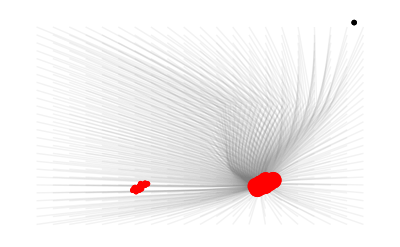
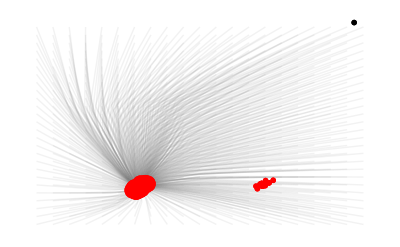
```mathematica
repeatedPhasePlot=Show[
TrajectoriesPlot[
repeated,
NetEncoder[{"Class",dfaRepeated["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@Table[#,10],
Level[DimensionReduction[repeated["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"][#,"OriginalData"]&/@Table[{x,y},{x,-10,10,1},{y,-5,20,1}],{-2}],
"Opacity"->0.1,
"Size"->Thick
],
ListPlot[{DimensionReduction[repeated["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"]@Table[0,8]},PlotMarkers->{"*", Large},PlotStyle->Black],
FixedPointPlot[repeated,If[#==0,1,2],"Size"->0.03],
FixedPointPlot[repeated,If[#==1,1,2],"Size"->0.01],
PlotRange->Full,
Axes->False
]&/@{0,1}
{-Graphics-,-Graphics-}
repeatedTypicalTraj=Show[
TrajectoriesPlot[
repeated,
NetEncoder[{"Class",dfaRepeated["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@{0,1,0,1,0,1,0,1,0,1,#,0,1,1,0,1,1,1,1},
Table[0,8],
"Opacity"->1,
"Color"->Green,
"Size"->Gray
],
FixedPointPlot[repeated,All],
ListPlot[{DimensionReduction[repeated["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"]@Table[0,8]},PlotMarkers->{"*", Large},PlotStyle->Black],
PlotRange->Full,
Axes->False
]&/@{0,1}
{-Graphics-,-Graphics-}

GraphicsGrid[{Join[{-Graphics-},repeatedPhasePlot],Join[{SpanFromAbove},repeatedTypicalTraj]},Frame->All]
-Graphics-
```

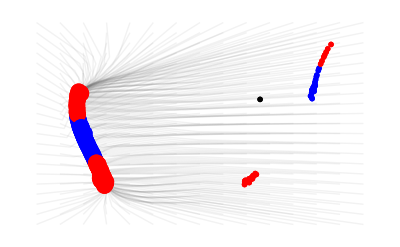
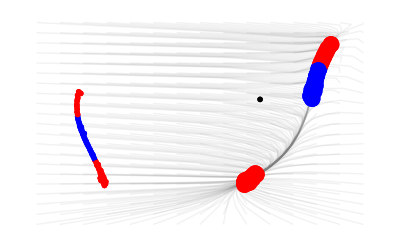
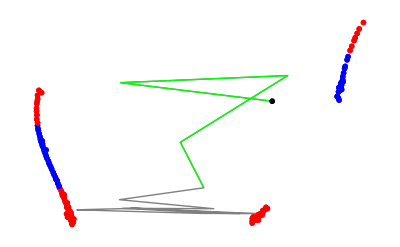
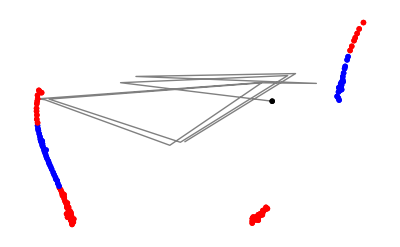
```mathematica
seqIdenficationPhasePlot=Show[
TrajectoriesPlot[
seqIdenfication,
NetEncoder[{"Class",dfaSeqIdenfication["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@Table[#,10],
Level[DimensionReduction[seqIdenfication["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"][#,"OriginalData"]&/@Table[{x,y},{x,-6,8,1},{y,-5,15,1}],{-2}],
"Opacity"->0.1,
"Size"->Thick
],
ListPlot[{DimensionReduction[seqIdenfication["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"]@Table[0,8]},PlotMarkers->{"*", Large},PlotStyle->Black],
FixedPointPlot[seqIdenfication,If[#==0,1,2],"Size"->0.03],
FixedPointPlot[seqIdenfication,If[#==1,1,2],"Size"->0.01],
PlotRange->Full,
Axes->False,
Boxed->False
]&/@{0,1}
{-Graphics-,-Graphics-}
seqIdenficationTypicalTraj1=Show[
TrajectoriesPlot[
seqIdenfication,
NetEncoder[{"Class",dfaSeqIdenfication["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@{0,1,0,1,0,1,0,1,1,1,0,0,0,1,1,0},
Table[0,8],
"Opacity"->1,
"Color"->Gray,
"Size"->Thick
],
TrajectoriesPlot[
seqIdenfication,
NetEncoder[{"Class",dfaSeqIdenfication["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@{0,1,0,1},
Table[0,8],
"Opacity"->1,
"Color"->Green,
"Size"->Thick
],
FixedPointPlot[seqIdenfication,All],
ListPlot[{DimensionReduction[seqIdenfication["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"]@Table[0,8]},PlotMarkers->{"*", Large},PlotStyle->Black],
PlotRange->Full,
Axes->False
]
-Graphics-
seqIdenficationTypicalTraj2=Show[
TrajectoriesPlot[
seqIdenfication,
NetEncoder[{"Class",dfaSeqIdenfication["Alphabet"],"UnitVector","Dimensions"->{"Varying"}}]@{0,1,0,0,1,0,0,0,0,1,1,0,1,0},
Table[0,8],
"Opacity"->1,
"Color"->Gray,
"Size"->Thick
],
FixedPointPlot[seqIdenfication,All],
ListPlot[{DimensionReduction[seqIdenfication["SamplingRun"],2,Method->"PrincipalComponentsAnalysis"]@Table[0,8]},PlotMarkers->{"*", Large},PlotStyle->Black],
PlotRange->Full,
Axes->False
]
-Graphics-
GraphicsGrid[{Join[{-Graphics-},seqIdenficationPhasePlot],{SpanFromAbove,seqIdenficationTypicalTraj1,seqIdenficationTypicalTraj2}},Frame->All]
-Graphics-
```